## Axion off-diagonal couplings to quarks and leptons

Goal: 
	Data analysis
	
Input: 
	output/yukawa_quark.m
	output/yukawa_lepton.m
	
Output:
	Figure 4
	Figure 5

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\2_Programming\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

WARNING! DO NOT EVALUATE THE WHOLE NOTEBOOK!

### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{861,2,3,3}

```mathematica
leptonData = <<"output/yukawa_lepton.m";
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData[[1]]]
Print["Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)"]
Dimensions[leptonData[[2]]]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{4323,2,3,3}

Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)

{3975,2,3,3}

### Find a set of c_P, c_M, convert to c_L, c_R

WARNING! THESE RESULTS HAVE BEEN SAVED! 
DO NOT EVALUATE AGAIN

```mathematica
(* 
	Scan the values for Subscript[c, L], Subscript[c, R] for all quarks 
	for different values of cM
	store in cuData, cdData
 *)
```

```mathematica
cMArray=Range[0.02,5.02,0.25]
With[{seed=0.001},
cuData={};
cdData={};
Do[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[yu];myd=Minors[yd];
AppendTo[cuData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==QuarkEffMass[yu,yd,myu,myd][#],{cP,cM+seed}]&)/@{"u","c","t"}],
{cM,cMArray}
]//Quiet
];
AppendTo[cdData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==QuarkEffMass[yu,yd,myu,myd][#],{cP,cM+seed}]&)/@{"d","s","b"}],
{cM,cMArray}
]//Quiet
],{i,Length[quarkData]}
]
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[cuData]
Dimensions[cdData]
```

```mathematica
(* 
	Scan the values for Subscript[c, L], Subscript[c, R] for all leptons
	for different values of cM
	store in clNHData, clIHData
 *)
```

```mathematica
With[{seed=0.001},
clNHData={};
Do[
yn = leptonData[[1]][[i, 1]]; ye = leptonData[[1]][[i,2]];myn=Minors[yn];mye=Minors[ye];
AppendTo[clNHData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==LeptonEffMass[yn,ye,myn,mye][#],{cP,cM+seed}]&)/@{"e","mu","tau"}],
{cM,cMArray}
]//Quiet
],{i,Length[leptonData[[1]]]}]
];//AbsoluteTiming
Clear[yn,ye,myn,mye];
Dimensions[clNHData]
```

{407.741,Null}

```mathematica
With[{seed=0.001},
clIHData={};
Do[
yn = leptonData[[2]][[i, 1]]; ye = leptonData[[2]][[i,2]];myn=Minors[yn];mye=Minors[ye];
AppendTo[clIHData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==LeptonEffMass[yn,ye,myn,mye][#],{cP,cM+seed}]&)/@{"e","mu","tau"}],
{cM,cMArray}
]//Quiet
],{i,Length[leptonData[[2]]]}]
];//AbsoluteTiming
Clear[yn,ye,myn,mye];
Dimensions[clIHData]
```

{398.896,Null}

{3975,21,3,2}

```mathematica
(* Export all evaluated result *)
```

```mathematica
(* Export["data/cLcR.m",{cMArray,cuData,cdData,clNHData,clIHData}] *)
```

data/cLcR.m

### Find the axion - fermions off-diagonal couplings

#### Loading necessary data

```mathematica
(* Import cL, cR calculated above *)
```

```mathematica
{cMArray,cuData,cdData,clNHData,clIHData}=<<"output/cLcR.m";
```

```mathematica
(* Get A matrices from yu, yd data *)
```

```mathematica
quarkAData = Table[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[quarkData[[i, 1]]];myd=Minors[quarkData[[i, 2]]];
QuarkAMatrices[yu, yd, myu, myd]
,{i,Length[quarkData]}
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[quarkAData]
```

{2.8157,Null}

{861,4,3,3}

```mathematica
leptonADataNH = Table[
yn = leptonData[[1]][[i, 1]]; ye = leptonData[[1]][[i,2]];myn=Minors[yn];mye=Minors[ye];
QuarkAMatrices[yn, ye, myn, mye]
,{i,Length[leptonData[[1]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataNH]
```

{14.1608,Null}

{4323,4,3,3}

```mathematica
leptonADataIH = Table[
yn = leptonData[[2]][[i, 1]]; ye = leptonData[[2]][[i,2]];myn=Minors[yn];mye=Minors[ye];
QuarkAMatrices[yn, ye, myn, mye]
,{i,Length[leptonData[[2]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataIH]
```

{13.0577,Null}

{3975,4,3,3}

#### Up Quark

```mathematica
cuData//Dimensions
```

{861,21,3,2}

```mathematica
data=cuData;
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]], whichC = 2 (* cR *),Δ=9},
output=Table[
quarkAData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, whichC]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ quarkAData[[k,2]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
output//Dimensions
```

{861,21,3,3}

Entry 12 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-10.3947,1.0737}

Histogram of the absolute value and the phase

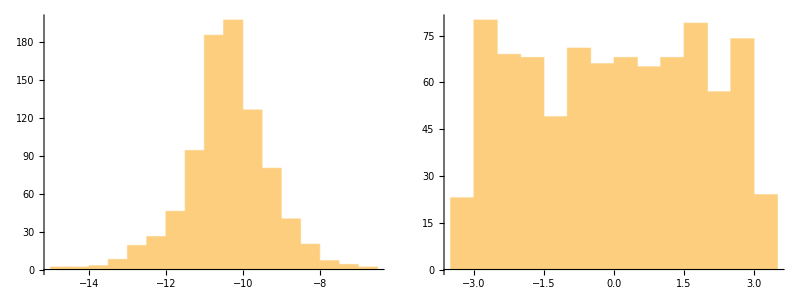

```mathematica
With[{cmpt=1, r = 1, c = 2},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 13 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-11.639,1.14668}

Histogram of the absolute value and the phase

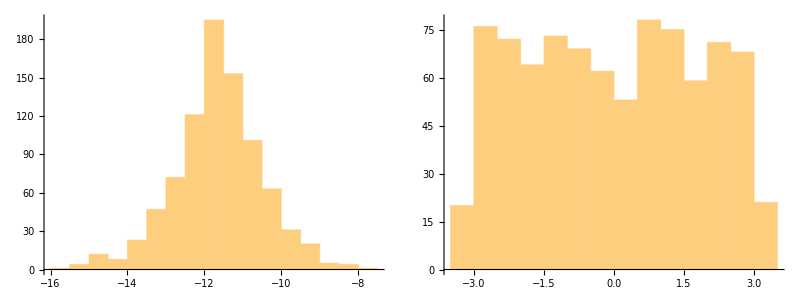

```mathematica
With[{cmpt=1, r = 1, c = 3},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 23 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-8.318,1.18301}

Histogram of the absolute value and the phase

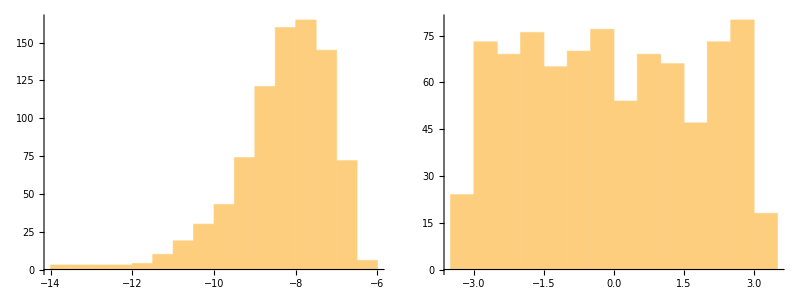

```mathematica
With[{cmpt=1, r = 2, c = 3},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

```mathematica
y12 = Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
colors=ColorData[97,"ColorList"];
```

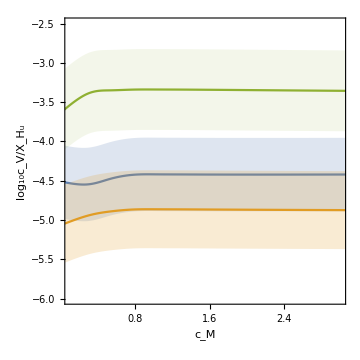

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{-6,-2.5}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_V/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23
]
```

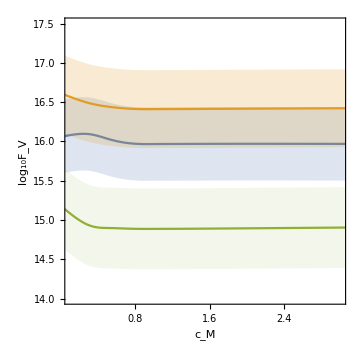

```mathematica
With[{σ0 =0.1,gSquared=1,Mpl=10^19,zir=10^8,Δ=9},
Fa=Mpl/(zir Sqrt[Δ-1]);
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{14.0,17.5}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_V"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y12),
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y13),
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y23)
]
]
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]], whichC = 2 (* cR *)},
outputDelta=Table[
quarkAData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, whichC]],Δ ],{whichQuark,3}] ].
ConjugateTranspose[ quarkAData[[k,2]] ],
{Δ,{7,9,11}},{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
output//Dimensions
```

{861,21,3,3}

```mathematica
outputDelta//Dimensions
```

{3,861,21,3,3}

```mathematica
y12 =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y12 =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,2]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y12 =Table[
 Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,2,3]]]],
{Δidx,3},{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y12//Dimensions
```

{3,21}

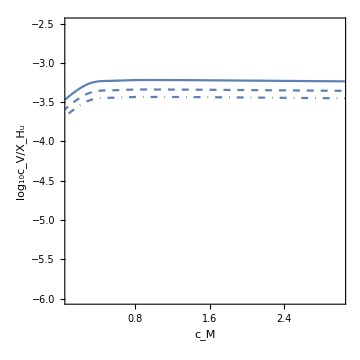

```mathematica
Show[
ListPlot[{{cMArray,#[[ 1]]}//Transpose,{cMArray,#[[ 2]]}//Transpose,{cMArray,#[[ 3]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{-6,-2.5}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_V/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],{colors[[1]],Dashed},{colors[[1]],DotDashed}}
]& @ y12
]
```

#### Down Quark

```mathematica
cdData//Dimensions
```

{861,21,3,2}

```mathematica
data=cdData;
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]], whichC = 2 (* cR *),Δ=9},
output=Table[
quarkAData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, whichC]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ quarkAData[[k,2]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
output//Dimensions
```

{861,21,3,3}

Entry 12 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-11.1177,1.17658}

Histogram of the absolute value and the phase

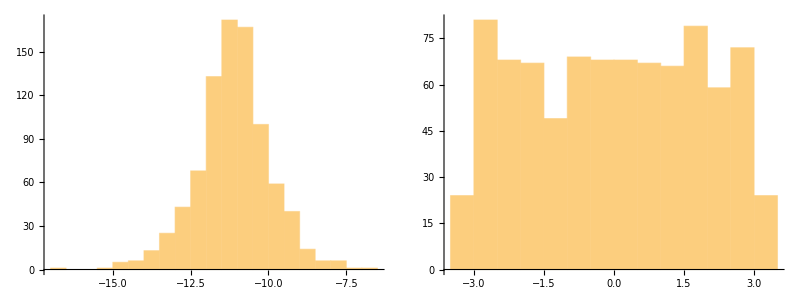

```mathematica
With[{cmpt=1, r = 1, c = 2},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 13 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-11.6835,1.12118}

Histogram of the absolute value and the phase

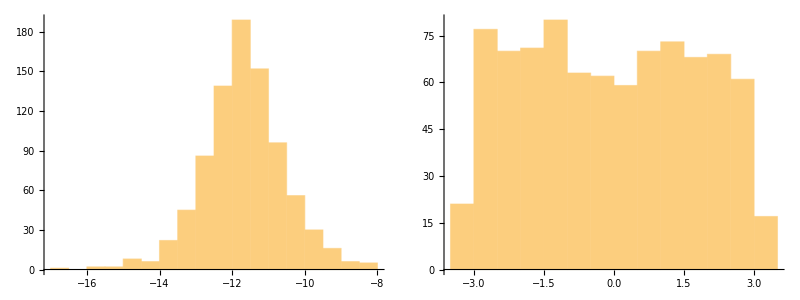

```mathematica
With[{cmpt=1, r = 1, c = 3},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 23 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-8.35649,1.23514}

Histogram of the absolute value and the phase

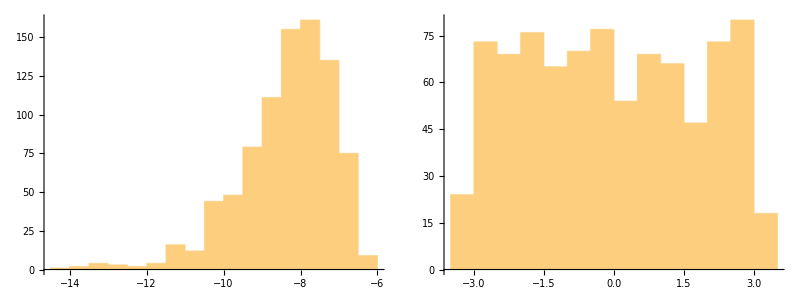

```mathematica
With[{cmpt=1, r = 2, c = 3},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

```mathematica
y12 = Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
colors=ColorData[97,"ColorList"];
```

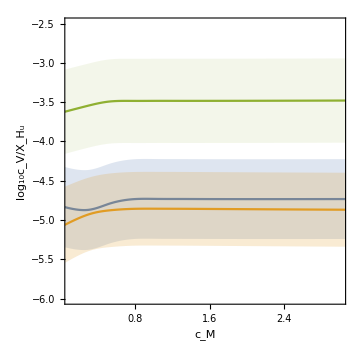

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{-6,-2.5}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_V/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23
]
```

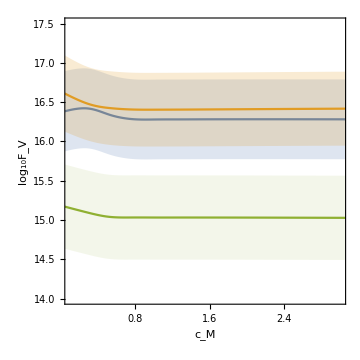

```mathematica
With[{σ0 =0.1,gSquared=1,Mpl=10^19,zir=10^8,Δ=9},
Fa=Mpl/(zir Sqrt[Δ-1]);
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{14.0,17.5}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_V"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y12),
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y13),
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y23)
]
]
```

#### Lepton Normal Hiearchy

```mathematica
clNHData//Dimensions
```

{4323,21,3,2}

```mathematica
leptonADataNH//Dimensions
```

{4323,4,3,3}

```mathematica
data=clNHData;
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]], whichC = 2 (* cR *),Δ=9},
output=Table[
leptonADataNH[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, whichC]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ leptonADataNH[[k,2]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
output//Dimensions
```

{4323,21,3,3}

Entry 12 of the axion coupling to the lepton with normal hierarchy

μ, σ of the log of the absolute values:

{-9.89905,1.11408}

Histogram of the absolute value and the phase

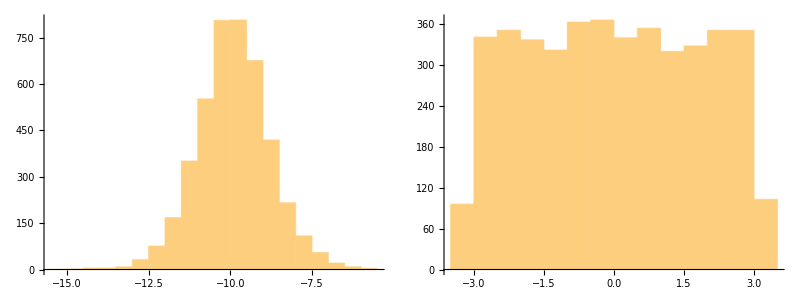

```mathematica
With[{cmpt=1, r = 1, c = 2},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the lepton with normal hierarchy"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 13 of the axion coupling to the lepton with normal hierarchy

μ, σ of the log of the absolute values:

{-10.2617,0.971968}

Histogram of the absolute value and the phase

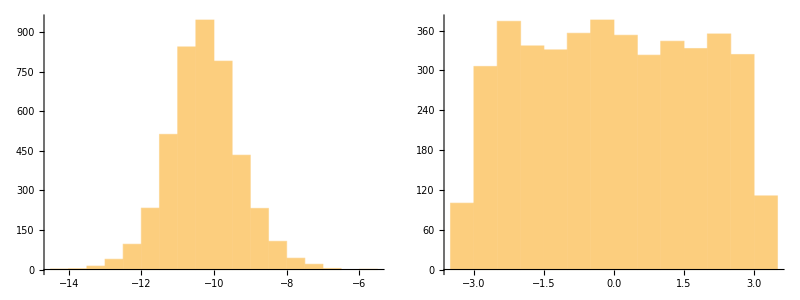

```mathematica
With[{cmpt=1, r = 1, c = 3},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the lepton with normal hierarchy"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 23 of the axion coupling to the lepton with normal hierarchy

μ, σ of the log of the absolute values:

{-7.37546,1.38244}

Histogram of the absolute value and the phase

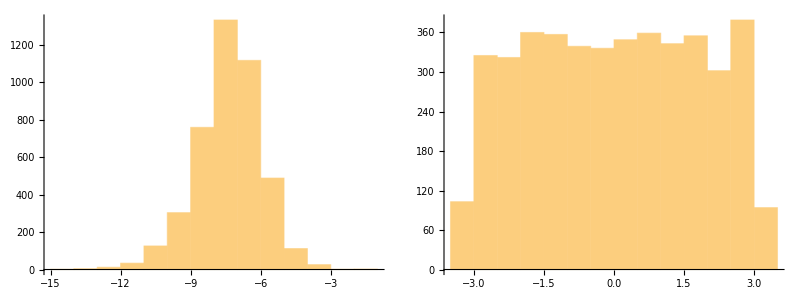

```mathematica
With[{cmpt=1, r = 2, c = 3},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the lepton with normal hierarchy"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

```mathematica
y12 = Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
colors=ColorData[97,"ColorList"];
```

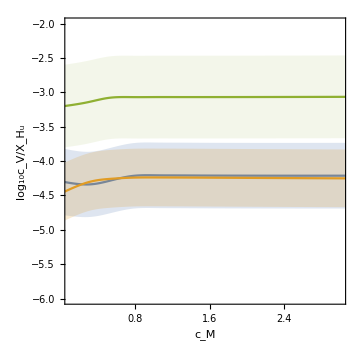

```mathematica
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{-6,-2}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_V/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23
]
```

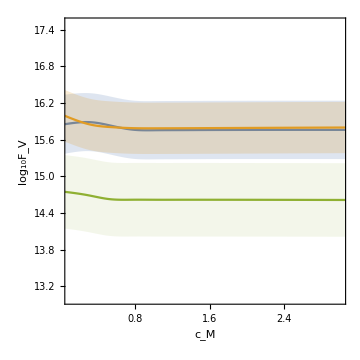

```mathematica
With[{σ0 =0.1,gSquared=1,Mpl=10^19,zir=10^8,Δ=9},
Fa=Mpl/(zir Sqrt[Δ-1]);
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{13.0,17.5}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_V"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y12),
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y13),
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y23)
]
]
```

#### Lepton Inverted Hiearchy

```mathematica
clIHData//Dimensions
```

{3975,21,3,2}

```mathematica
leptonADataIH//Dimensions
```

{3975,4,3,3}

```mathematica
data=clIHData;
```

```mathematica
With[
{kMax = Dimensions[data][[1]], cmTotal =Dimensions[data][[2]], whichC = 2 (* cR *),Δ=9},
output=Table[
leptonADataIH[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ data[[k, cmpt, whichQuark, whichC]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ leptonADataIH[[k,2]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
output//Dimensions
```

{3975,21,3,3}

Entry 12 of the axion coupling to the lepton with inverted hierarchy

μ, σ of the log of the absolute values:

{-9.90837,1.10798}

Histogram of the absolute value and the phase

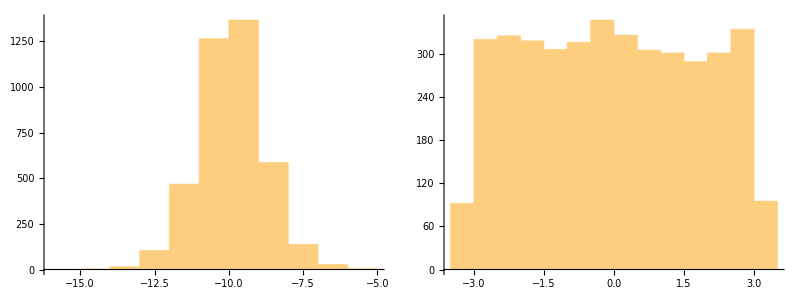

```mathematica
With[{cmpt=1, r = 1, c = 2},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the lepton with inverted hierarchy"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 13 of the axion coupling to the lepton with inverted hierarchy

μ, σ of the log of the absolute values:

{-10.2462,0.969734}

Histogram of the absolute value and the phase

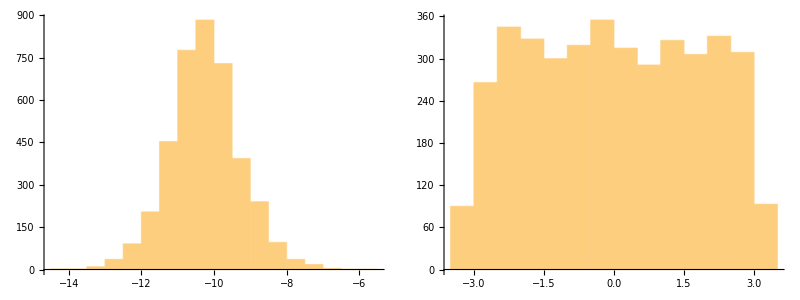

```mathematica
With[{cmpt=1, r = 1, c = 3},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the lepton with inverted hierarchy"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 23 of the axion coupling to the lepton with inverted hierarchy

μ, σ of the log of the absolute values:

{-7.35367,1.387}

Histogram of the absolute value and the phase

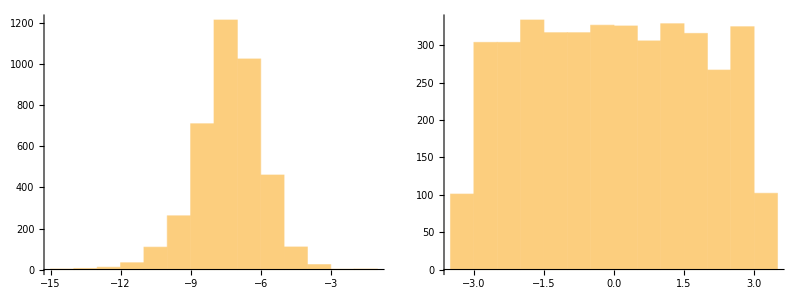

```mathematica
With[{cmpt=1, r = 2, c = 3},
sample = output[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the lepton with inverted hierarchy"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

```mathematica
y12 = Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y13= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
y23= Table[
Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],
{cmpt,Dimensions[data][[2]]}
];
```

```mathematica
colors=ColorData[97,"ColorList"];
```

a-l-l (inverted hierarchy) coupling c_12(blue), c_13(orange) and c_23(green)

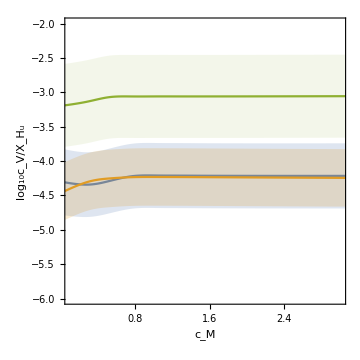

```mathematica
Print["a-l-l (inverted hierarchy) coupling c_12(blue), c_13(orange) and c_23(green)"];
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{-6,-2}},ImageSize->Medium,FrameLabel->{"c_M","log_10c_V/X_H_u"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ y12,
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @ y13,
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ y23
]
```

a-l-l (inverted hierarchy) coupling F_12(blue), F_13(orange) and F_23(green)

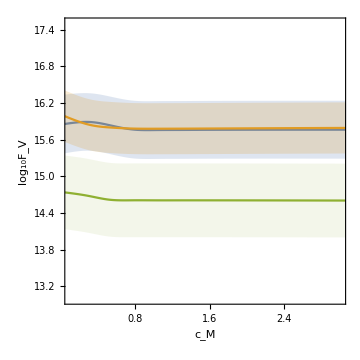

```mathematica
Print["a-l-l (inverted hierarchy) coupling F_12(blue), F_13(orange) and F_23(green)"];
With[{σ0 =0.1,gSquared=1,Mpl=10^19,zir=10^8,Δ=9},
Fa=Mpl/(zir Sqrt[Δ-1]);
Show[
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,PlotRange->{{0.1,3.},{13.0,17.5}},ImageSize->Medium,FrameLabel->{"c_M","log_10F_V"},AspectRatio->1,
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[1]]]
]& @ ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y12),
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.2],colors[[2]]]
]& @  ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y13),
ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
Joined->True,Frame->True,InterpolationOrder->3,
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.1],colors[[3]]]
]& @ ( ({Log10[Fa/(gSquared σ0)],0}-#)&/@y23)
]
]
```